```mathematica
(* created at 2015/06/14 *)
```

```mathematica
SeedRandom[0]
```

```mathematica
argList[f_,dt_]:=Table[Arg[f[t]],{t,0,2π,dt}];
absList[f_,dt_]:=Table[Abs[f[t]],{t,0,2π,dt}];
reList[f_,dt_]:=Table[Re[f[t]],{t,0,2π,dt}];
correct[li_List]:=Rest[li]+Accumulate[Piecewise[{{-2π,#≥π},{2π,#≤-π}}]&/@Differences[li]];
numberOfExtremum[li_List]:=Length[Select[Differences[li]*RotateRight[Differences[li]],#≤0&]];
inclinationList[f_,dt_]:=Table[Arg[f[t+dt]-c[t]],{t,0,2π,dt}];
breakNumber[li_List]:=Length[Select[Differences[li],#≤-π&]]-Length[Select[Differences[li],#≥π&]] ;
```

```mathematica
normalize[p_,a_,b_]:=If[b-a≠0,(p-a)/(b-a),ComplexInfinity]
cross0Q[x_,y_]:=If[x≠y,IntervalMemberQ[Interval[{x,y}],0],False]
intervalIntersectionQ[a_,b_]:=!((a<0&&b<0)||(a>1&&b>1))
complexToVector[x_]:={Re[x],Im[x]}
cross01Q[p2_,q2_]:=If[cross0Q[Im[p2],Im[q2]]&&0≤Re[(Im[p2] q2-Im[q2] p2)/(Im[p2]-Im[q2])]≤1,True,If[Im[p2]==0&&Im[q2]==0,intervalIntersectionQ[Im[p2],Im[q2]],False]]
crossQ[{{p_,q_},{a_,b_}}]:=If[a==b,If[p==q,a==p,cross01Q[normalize[a,p,q],normalize[b,p,q]]],cross01Q[normalize[p,a,b],normalize[q,a,b]]]
curveCrossQ[{{p_,q_},{a_,b_}}]:=If[q≠a&&b≠p,crossQ[{{p,q},{a,b}}],False]
```

```mathematica
lowAmpLi={1,1,1,1,1,0,0,0,0,0};
highAmpLi={0,0,0,0,0,1,1,1,1,1};
```

```mathematica
f[ampLi_List]:=Module[{rotLi=RandomReal[{0,2π},{Length[ampLi]}]},∑_(k=1)^Length[ampLi] ampLi⟦k⟧ Exp[ⅈ k (#-rotLi⟦k⟧)] &];
```

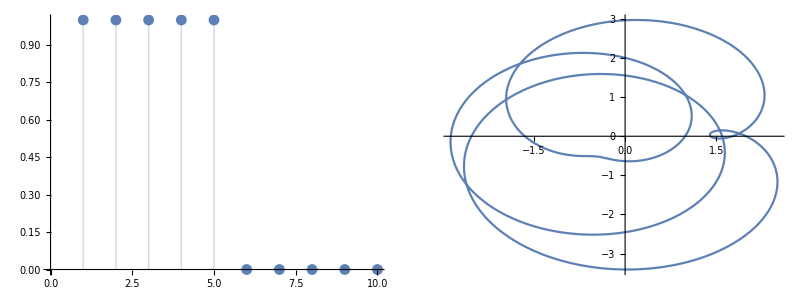

```mathematica
c=f[lowAmpLi];
Grid[{{
ListPlot[lowAmpLi,Filling->Bottom,PlotRange->{0,All}],
ParametricPlot[{Re[#],Im[#]}&[c[t]],{t,0,2π},PlotRange->All]
}}]
```

Rotation:

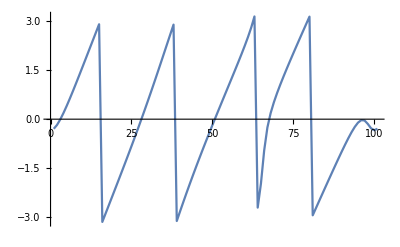

4

```mathematica
(* NumberOfRotation *)
numberOfRotation[f_, dt_]:=breakNumber[inclinationList[f,dt]]
Print["Rotation:"]
ListLinePlot[inclinationList[c,(2π)/100]]
numberOfRotation[c,(2π)/100]
```

ArgExtremum:

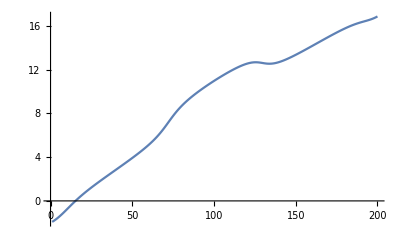

1

```mathematica
(* NumberOfArgExtremum *)
numberOfArgExtremum[f_,dt_]:=numberOfExtremum[correct[argList[f,dt]]]/2;
Print["ArgExtremum:"]
ListLinePlot[correct[argList[c,(2π)/200]]]
numberOfArgExtremum[c,(2π)/200]
```

AbsExtremum:

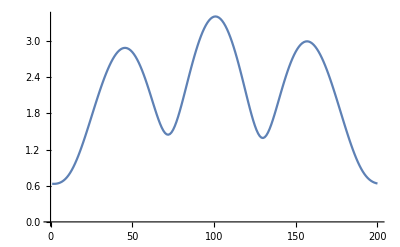

3

```mathematica
(* NumberOfAbsExtremum *)
Print["AbsExtremum:"]
ListLinePlot[correct[absList[c,(2π)/200]]]
numberOfAbsExtremum[f_,dt_]:=numberOfExtremum[correct[absList[f,dt]]]/2
numberOfAbsExtremum[c,(2π)/200]
```

ReExtremum:

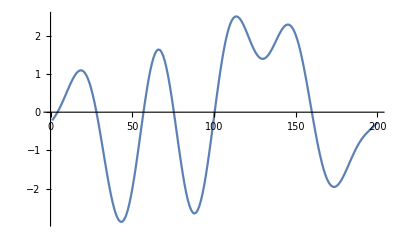

4

```mathematica
(* NumberOfReExtremum *)
Print["ReExtremum:"]
ListLinePlot[correct[reList[c,(2π)/200]]]
numberOfReExtremum[f_,dt_]:=numberOfExtremum[correct[reList[f,dt]]]/2
numberOfReExtremum[c,(2π)/200]
```

```mathematica
(* Sound *)
Play[Re[c[440*2π*t]],{t,0,1}]
```

-Graphics-

```mathematica
SeedRandom[0]
```

```mathematica
norList1={};
noargeList1={};
noabseList1={};
noreList1={};
lenList1={};
noiList1={};
Do[
c=f[lowAmpLi];

(* NumberOfRotation *)
nor=numberOfRotation[c,(2π)/100];
AppendTo[norList1,nor];

(* NumberOfArgExtremum *)
noarge=numberOfArgExtremum[c,(2π)/200];
AppendTo[noargeList1,noarge];

(* NumberOfAbsExtremum *)
noabse=numberOfAbsExtremum[c,(2π)/200];
AppendTo[noabseList1,noabse];

(* NumberOfReExtremum *)
nore=numberOfReExtremum[c,(2π)/200];
AppendTo[noreList1,nore];

(* Length *)
dt=(2π)/500;
curveLength=Sum[Abs[c[t+dt]-c[t]],{t,0,2π,dt}];
AppendTo[lenList1,curveLength];

(* NumberOfIntersection *)
dt=(2π)/200;
li=Most[Table[c[t],{t,0,2π,dt}]];
lines={li,RotateLeft[li]}ᵀ;
noi=Count[curveCrossQ/@Subsets[lines,{2}],True];
AppendTo[noiList1,noi];
,{100}]
```

```mathematica
SeedRandom[0]
```

```mathematica
norList2={};
noargeList2={};
noabseList2={};
noreList2={};
lenList2={};
noiList2={};
Do[
c=f[highAmpLi];

(* NumberOfRotation *)
nor=numberOfRotation[c,(2π)/100];
AppendTo[norList2,nor];

(* NumberOfArgExtremum *)
noarge=numberOfArgExtremum[c,(2π)/200];
AppendTo[noargeList2,noarge];

(* NumberOfAbsExtremum *)
noabse=numberOfAbsExtremum[c,(2π)/200];
AppendTo[noabseList2,noabse];

(* NumberOfReExtremum *)
nore=numberOfReExtremum[c,(2π)/200];
AppendTo[noreList2,nore];

(* Length *)
dt=(2π)/500;
curveLength=Sum[Abs[c[t+dt]-c[t]],{t,0,2π,dt}];
AppendTo[lenList2,curveLength];

(* NumberOfIntersection *)
dt=(2π)/200;
li=Most[Table[c[t],{t,0,2π,dt}]];
lines={li,RotateLeft[li]}ᵀ;
noi=Count[curveCrossQ/@Subsets[lines,{2}],True];
AppendTo[noiList2,noi];
,{100}]
```

```mathematica
displayVariable[var_String]:=var<>"="<>ToString[Symbol[var]]
```

```mathematica
displayVariable["norList1"]
displayVariable["noargeList1"]
displayVariable["noabseList1"]
displayVariable["noreList1"]
displayVariable["lenList1"]
displayVariable["noiList1"]
displayVariable["norList2"]
displayVariable["noargeList2"]
displayVariable["noabseList2"]
displayVariable["noreList2"]
displayVariable["lenList2"]
displayVariable["noiList2"]
```

norList1={4, 4, 4, 4, 5, 4, 4, 4, 4, 4, 4, 4, 4, 5, 4, 4, 4, 5, 4, 3, 4, 4, 4, 4, 5, 4, 4, 4, 4, 4, 5, 4, 4, 4, 5, 5, 4, 5, 4, 4, 4, 5, 4, 4, 4, 4, 4, 4, 5, 4, 4, 4, 5, 4, 5, 5, 5, 4, 3, 4, 4, 4, 4, 4, 5, 4, 4, 4, 5, 5, 4, 4, 4, 5, 5, 4, 4, 4, 4, 4, 4, 4, 4, 5, 4, 4, 4, 4, 5, 4, 4, 4, 4, 4, 4, 5, 4, 4, 4, 4}

noargeList1={1, 3, 1, 1, 3, 1, 0, 1, 1, 1, 1, 0, 1, 3, 0, 1, 0, 3, 0, 0, 1, 2, 0, 1, 3, 1, 1, 1, 2, 0, 3, 1, 1, 2, 3, 3, 1, 3, 2, 1, 1, 3, 1, 2, 0, 1, 0, 1, 2, 0, 0, 1, 3, 1, 3, 3, 2, 0, 0, 0, 1, 2, 2, 0, 2, 1, 1, 0, 3, 2, 0, 0, 0, 2, 3, 0, 1, 0, 1, 1, 2, 1, 1, 2, 3, 0, 1, 0, 2, 1, 1, 1, 1, 2, 2, 2, 1, 0, 0, 1}

noabseList1={3, 4, 3, 4, 4, 4, 4, 3, 3, 4, 4, 3, 3, 3, 3, 4, 4, 3, 3, 4, 4, 3, 4, 3, 3, 4, 3, 3, 2, 3, 3, 4, 4, 3, 4, 4, 3, 3, 4, 3, 4, 4, 4, 3, 4, 4, 4, 4, 4, 3, 3, 4, 4, 4, 4, 4, 3, 4, 4, 3, 4, 3, 3, 4, 4, 4, 3, 3, 4, 4, 4, 4, 4, 4, 3, 4, 3, 4, 4, 3, 4, 4, 3, 4, 3, 3, 3, 4, 4, 3, 4, 3, 3, 3, 3, 4, 4, 3, 3, 3}

noreList1={4, 5, 4, 4, 5, 4, 4, 4, 4, 5, 4, 4, 4, 5, 4, 4, 4, 5, 4, 4, 4, 5, 4, 4, 5, 4, 4, 4, 5, 4, 5, 4, 4, 5, 5, 5, 4, 5, 4, 4, 4, 5, 4, 4, 4, 4, 4, 4, 5, 4, 4, 4, 5, 4, 5, 5, 5, 4, 4, 4, 4, 5, 4, 4, 5, 4, 4, 4, 5, 5, 4, 4, 4, 5, 5, 4, 5, 4, 4, 4, 4, 4, 4, 5, 4, 4, 4, 4, 5, 4, 4, 4, 4, 5, 5, 5, 4, 4, 4, 4}

lenList1={42.5905, 40.233, 43.3962, 44.56, 39.5003, 42.7257, 45.4581, 45.0894, 43.0187, 40.6784, 41.2669, 45.003, 44.4825, 39.4387, 42.7831, 43.4522, 39.7459, 39.4495, 44.769, 42.6694, 41.3529, 40.2416, 42.7287, 43.3412, 39.4341, 43.5729, 42.2621, 45.3243, 41.8536, 44.2912, 39.4648, 41.6255, 43.379, 40.9062, 40.7196, 40.1668, 43.4442, 39.4115, 42.1799, 42.7547, 41.3091, 40.7567, 42.862, 41.2039, 46.3269, 43.9989, 45.6002, 41.3772, 39.1199, 46.0371, 45.861, 45.3588, 40.9202, 43.0641, 39.5365, 40.729, 40.3603, 45.7198, 42.0834, 43.7042, 43.313, 41.5668, 43.2229, 45.2468, 38.7721, 42.7447, 44.0573, 44.3677, 40.0446, 40.4472, 43.2603, 41.9502, 45.5534, 39.6832, 39.3067, 45.3132, 40.8732, 45.7078, 43.7207, 44.6621, 41.7024, 45.1997, 45.0306, 38.7603, 41.8245, 43.8222, 44.4134, 44.8968, 38.7509, 44.9656, 41.163, 42.373, 43.2302, 40.5427, 41.6351, 39.5286, 42.2755, 40.9792, 44.6536, 44.7305}

noiList1={7, 3, 9, 5, 8, 5, 7, 7, 5, 5, 3, 7, 9, 6, 7, 7, 7, 4, 7, 4, 5, 3, 5, 9, 6, 5, 5, 9, 5, 7, 6, 5, 3, 5, 6, 6, 9, 6, 5, 9, 5, 6, 5, 7, 9, 5, 7, 5, 10, 7, 9, 9, 8, 7, 4, 6, 6, 7, 6, 7, 7, 5, 5, 5, 8, 5, 7, 7, 6, 6, 5, 7, 5, 6, 4, 7, 5, 7, 7, 7, 5, 9, 9, 8, 5, 9, 9, 7, 6, 9, 5, 7, 9, 3, 5, 12, 3, 9, 9, 9}

norList2={9, 8, 8, 8, 8, 9, 8, 8, 9, 9, 8, 9, 9, 8, 9, 8, 9, 8, 9, 8, 9, 8, 9, 8, 9, 8, 9, 8, 8, 9, 8, 8, 9, 8, 9, 8, 8, 9, 9, 9, 8, 8, 8, 9, 7, 7, 8, 8, 9, 8, 8, 8, 8, 9, 8, 9, 9, 9, 9, 8, 8, 9, 9, 8, 9, 8, 8, 9, 8, 8, 8, 8, 9, 9, 9, 8, 9, 7, 8, 8, 9, 8, 9, 8, 8, 8, 9, 9, 9, 9, 8, 8, 9, 7, 9, 8, 8, 9, 9, 8}

noargeList2={1, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 1, 0, 0, 0, 0, 1, 0, 0, 2, 2, 1, 1, 0, 1, 0, 0, 1, 0, 1, 0, 0, 0, 0, 2, 0, 0, 0, 1, 2, 1, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 2, 0, 1, 2, 1, 0, 1, 2, 1, 0, 0, 0, 0, 0, 0, 0, 0, 2, 0, 2, 0, 1, 0, 1, 1, 1, 0, 0, 0, 0, 0, 1, 1, 0, 0, 1, 0, 0, 1, 1, 0, 0, 1, 0, 0}

noabseList2={4, 3, 4, 4, 3, 3, 4, 4, 3, 3, 3, 4, 4, 3, 3, 4, 3, 4, 3, 3, 4, 4, 3, 3, 3, 3, 3, 4, 3, 3, 3, 4, 4, 3, 4, 2, 4, 4, 3, 4, 4, 4, 3, 3, 4, 4, 4, 3, 3, 3, 3, 3, 3, 4, 4, 4, 4, 3, 3, 3, 3, 4, 2, 4, 4, 4, 4, 4, 3, 3, 4, 4, 3, 4, 3, 3, 4, 4, 3, 3, 3, 4, 3, 4, 4, 3, 4, 3, 3, 3, 3, 4, 4, 3, 4, 4, 3, 3, 3, 3}

noreList2={9, 8, 8, 10, 8, 9, 8, 8, 9, 9, 9, 9, 9, 8, 9, 8, 9, 9, 9, 9, 9, 8, 9, 9, 9, 9, 9, 8, 8, 9, 9, 8, 9, 8, 9, 9, 8, 9, 9, 9, 9, 8, 8, 9, 8, 7, 8, 8, 9, 8, 8, 8, 8, 9, 9, 9, 9, 9, 9, 9, 8, 9, 9, 8, 9, 8, 9, 9, 9, 8, 9, 9, 9, 9, 9, 9, 9, 8, 9, 8, 9, 8, 9, 8, 8, 8, 9, 9, 9, 9, 8, 9, 9, 8, 9, 8, 8, 9, 9, 9}

lenList2={100.386, 99.0532, 97.8895, 94.3667, 100.417, 110.041, 104.998, 97.6651, 99.7812, 105.752, 100.016, 95.0749, 104.315, 108.186, 109.58, 102.547, 102.925, 92.7632, 108.628, 99.931, 106.502, 102.326, 105.154, 107.809, 104.344, 103.928, 108.562, 104.703, 106.011, 107.834, 98.7881, 104.418, 107.336, 108.123, 104.432, 101.511, 110.685, 110.719, 101.758, 98.7448, 93.8796, 103.654, 105.942, 105.253, 100.235, 101.009, 105.568, 100.171, 110.119, 105.227, 105.262, 105.976, 105.426, 104.429, 95.2606, 90.5606, 105.146, 101., 100.971, 105.817, 101.437, 106.78, 102.945, 101.389, 107.54, 107.594, 96.5218, 103.984, 100.54, 102.146, 100.706, 103.154, 101.967, 107.52, 101.725, 104.677, 89.1337, 99.5509, 100.737, 94.783, 105.765, 104.992, 109.301, 110.18, 109.789, 104.789, 97.6916, 100.867, 103.573, 102.785, 100.552, 105.478, 110.192, 92.8597, 105.754, 107.231, 103.234, 108.344, 97.7656, 105.199}

noiList2={18, 17, 15, 17, 17, 18, 15, 13, 22, 16, 19, 30, 18, 19, 18, 25, 20, 21, 18, 16, 28, 17, 20, 31, 20, 21, 28, 17, 19, 26, 17, 21, 16, 19, 22, 17, 33, 22, 22, 18, 27, 15, 17, 20, 18, 20, 17, 17, 24, 19, 23, 17, 19, 20, 15, 20, 20, 20, 18, 20, 21, 22, 22, 15, 18, 23, 21, 18, 21, 19, 25, 19, 18, 32, 20, 19, 26, 12, 20, 17, 22, 21, 22, 21, 35, 17, 16, 20, 20, 22, 13, 23, 22, 19, 22, 17, 17, 34, 22, 21}

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
resultPlot[list1_,list2_]:=ErrorListPlot[{{{1,Mean[list1]},ErrorBar[{Min[list1]-Mean[list1],Max[list1]-Mean[list1]}]},{{2,Mean[list2]},ErrorBar[{Min[list2]-Mean[list2],Max[list2]-Mean[list2]}]}},PlotRange->{{0.5,2.5},{0,All}},AspectRatio->2,Ticks->{{{1,"OverTilde[s_1](t)"},{2,"OverTilde[s_2](t)"}},Automatic},LabelStyle->(FontSize->20)]
```

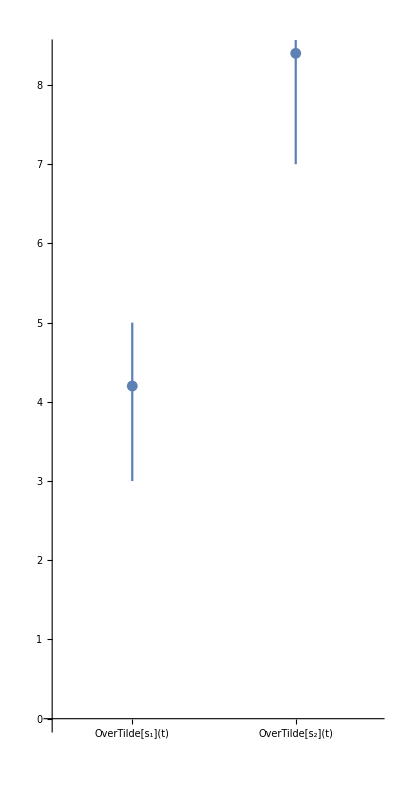

```mathematica
resultPlot[norList1,norList2]
```

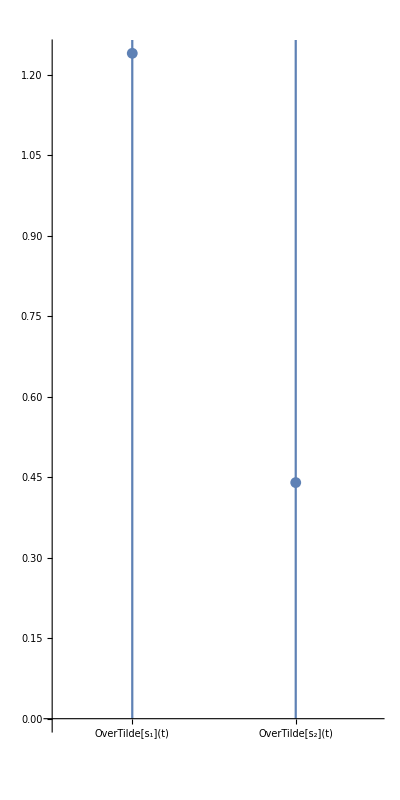

```mathematica
resultPlot[noargeList1,noargeList2]
```

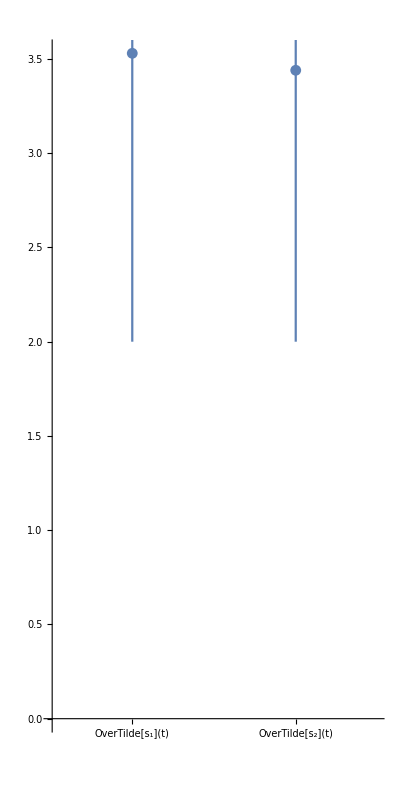

```mathematica
resultPlot[noabseList1,noabseList2]
```

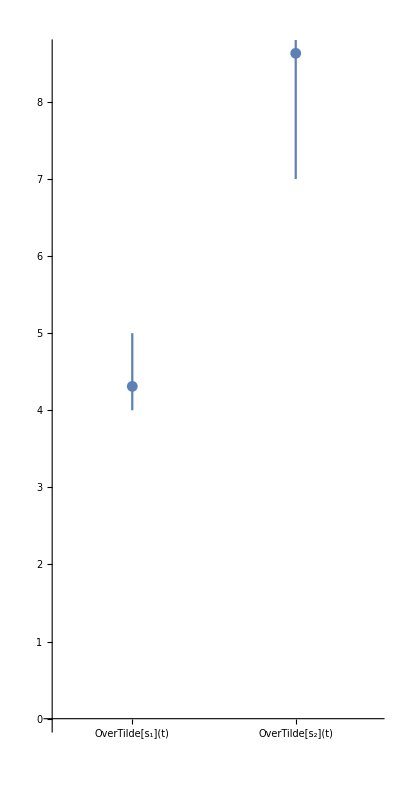

```mathematica
resultPlot[noreList1,noreList2]
```

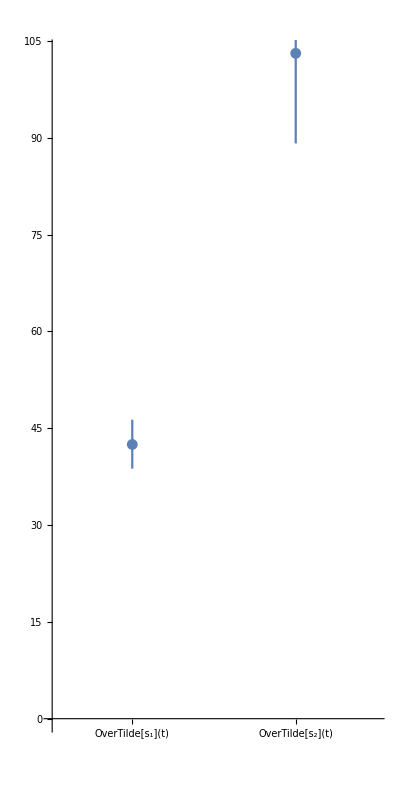

```mathematica
resultPlot[lenList1,lenList2]
```

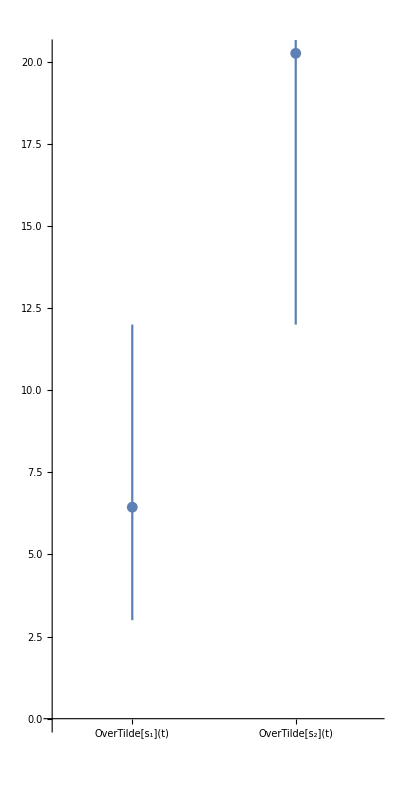

```mathematica
resultPlot[noiList1,noiList2]
```